```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/tomikbaikie/MIT Dropbox/Tomi Baikie/Tomi/Projects/BIO_Methods/BIO_Photodegredation_Sites/Data

```mathematica
converttoOD[data_]:=Module[{x,y,selection,datahold}, 
datahold=data; 
datahold = -Log[10,datahold+1];
Return[datahold];
]
```

```mathematica
(* Import Data *)
```

```mathematica
or1names=FileNames["./Oxygen_Removal/a_psi_minusoxygen/meas/*"];
or2names=FileNames["./Oxygen_Removal/a_psi_minusoxygen_1/meas/*"];
or3names=FileNames["./Oxygen_Removal/a_psi_minusoxygen_2/meas/*"];
or4names=FileNames["./Oxygen_Removal/a_psi_minusoxygen_3/meas/*"];

or1namesav=FileNames["./Oxygen_Removal/a_psi_minusoxygen/*.wtf"];
or2namesav=FileNames["./Oxygen_Removal/a_psi_minusoxygen_1/*.wtf"];
or3namesav=FileNames["./Oxygen_Removal/a_psi_minusoxygen_2/*.wtf"];
or4namesav=FileNames["./Oxygen_Removal/a_psi_minusoxygen_3/*.wtf"];

monomeric1av = FileNames["./Monomeric/2/meas/*.wtf"];
monomeric2av = FileNames["./Monomeric/3/meas/*.wtf"];
monomeric3av = FileNames["./Monomeric/4/meas/*.wtf"];

monomeric1names= FileNames["./Monomeric/2/meas/*.wtf"];
monomeric2names= FileNames["./Monomeric/3/meas/*.wtf"];
monomeric3names= FileNames["./Monomeric/4/meas/*.wtf"];

psi0p2mWnames=FileNames["./PSI/PSI_0p2mW/*"];
psi0p35mWnames=FileNames["./PSI/PSI_0p35mW/*"];
psi0p45mWnames=FileNames["./PSI/PSI_0p45mW/PSI/meas/*"];

psi1names=FileNames["./PSI/PSI_1/meas/*"];
psi2names=FileNames["./PSI/PSI_2/meas/*"];
psi3names=FileNames["./PSI/PSI_3/meas/*"];

psi1namesav=FileNames["./PSI/PSI_1/*.wtf"];
psi2namesav=FileNames["./PSI/PSI_2/*.wtf"];
psi3namesav=FileNames["./PSI/PSI_3/*.wtf"];

psimv1names=FileNames["./PSI_MV/PSI_2_MV_1mM/results/meas/*.wtf"];
psimv2names=FileNames["./PSI_MV/PSI_3_MV_1mM/results/meas/*.wtf"];
psimv3names=FileNames["./PSI_MV/PSI_4_MV_1mM/results/meas/*.wtf"];

psimv1namesav=FileNames["./PSI_MV/PSI_2_MV_1mM/*.wtf"];
psimv2namesav=FileNames["./PSI_MV/PSI_3_MV_1mM/*.wtf"];
psimv3namesav=FileNames["./PSI_MV/PSI_4_MV_1mM/*.wtf"];

ormv1names=FileNames["./Oxygen_Removal_MV/a_psi_minusoxygen_25mM_MV_1/meas/*"];
ormv2names=FileNames["./Oxygen_Removal_MV/a_psi_minusoxygen_5mM_MV_2/meas/*"];
ormv3names=FileNames["./Oxygen_Removal_MV/a_psi_minusoxygen_5mM_MV_3/meas/*"];

ormv1namesav=FileNames["./Oxygen_Removal_MV/a_psi_minusoxygen_5mM_MV_1/*.wtf"];
ormv2namesav=FileNames["./Oxygen_Removal_MV/a_psi_minusoxygen_5mM_MV_2/*.wtf"];
ormv3namesav=FileNames["./Oxygen_Removal_MV/a_psi_minusoxygen_5mM_MV_3/*.wtf"];
```

```mathematica
(* Data Processing *)
```

```mathematica
datamould2[data_]:=Module[{times,wavelengths,data2,data1}, 
times=data[[1,2;;]];
data1= data[[2;;]];
wavelengths=Transpose[data1][[1]];
data1=Transpose[Transpose[data1][[2;;]]];
data2=Transpose[{times,data1[[#]]}]&/@Range[Length[data1]];
data2=Table[Flatten[#,1]&/@Transpose[{wavelengths,Transpose[data2][[i]]}],{i,1,Length[Transpose[data1]]}];
data2=Flatten[data2,1];
data2=Select[data2,#[[1]]!= 0&];
Return[data2];
]
```

```mathematica
monomeric1avd=Import[#]&/@monomeric1av;
monomeric1namesd=Import[#]&/@monomeric1names;
monomericdata1={datamould2[monomeric1avd[[1]]],datamould2[monomeric1namesd[[3]]],datamould2[monomeric1namesd[[4]]],datamould2[monomeric1namesd[[5]]],datamould2[monomeric1namesd[[5]]]};

monomeric2avd=Import[#]&/@monomeric2av;
monomeric2namesd=Import[#]&/@monomeric2names;
monomericdata2={datamould2[monomeric2avd[[1]]],datamould2[monomeric2namesd[[3]]],datamould2[monomeric2namesd[[4]]],datamould2[monomeric2namesd[[5]]],datamould2[monomeric2namesd[[5]]]};

monomeric3avd=Import[#]&/@monomeric3av;
monomeric3namesd=Import[#]&/@monomeric3names;
monomericdata3={datamould2[monomeric3avd[[1]]],datamould2[monomeric3namesd[[3]]],datamould2[monomeric3namesd[[4]]],datamould2[monomeric3namesd[[5]]],datamould2[monomeric3namesd[[5]]]};
```

```mathematica
ormv1data=Import[#]&/@ormv1names;
ormv1data={datamould2[ormv1data[[3]]],datamould2[ormv1data[[4]]],datamould2[ormv1data[[5]]],datamould2[ormv1data[[6]]]};
ormv2data=Import[#]&/@ormv2names;
ormv2data={datamould2[ormv2data[[3]]],datamould2[ormv2data[[4]]],datamould2[ormv2data[[5]]],datamould2[ormv2data[[6]]]};
ormv3data=Import[#]&/@ormv3names;
ormv3data={datamould2[ormv3data[[3]]],datamould2[ormv3data[[4]]],datamould2[ormv3data[[5]]],datamould2[ormv3data[[6]]]};
```

```mathematica
or1dataav=Import[#]&/@or1namesav;
or2dataav=Import[#]&/@or2namesav;
or3dataav=Import[#]&/@or3namesav;
or4dataav=Import[#]&/@or4namesav;
ordataav={datamould2[or1dataav[[1]]],datamould2[or2dataav[[1]]],datamould2[or3dataav[[1]]],datamould2[or4dataav[[1]]]};
```

```mathematica
ormv1dataavor=Import[#]&/@ormv1namesav;
ormv2dataavor=Import[#]&/@ormv2namesav;
ormv3dataavor=Import[#]&/@ormv3namesav;
ormvdataavor={datamould2[ormv1dataavor[[1]]],datamould2[ormv2dataavor[[1]]],datamould2[ormv3dataavor[[1]]]};
```

```mathematica
psi1datasav=Import[#]&/@psi1namesav;
psi2datasav=Import[#]&/@psi2namesav;
psi3datasav=Import[#]&/@psi3namesav;
psidataav={datamould2[psi1datasav[[1]]],datamould2[psi2datasav[[1]]],datamould2[psi3datasav[[1]]]};
```

```mathematica
psimv1dataav=Import[#]&/@psimv1namesav;
psimv2dataav=Import[#]&/@psimv2namesav;
psimv3dataav=Import[#]&/@psimv3namesav;
psimvdataav={datamould2[psimv1dataav[[1]]],datamould2[psimv2dataav[[1]]],datamould2[psimv3dataav[[1]]]};
```

```mathematica
psimv1data=Import[#]&/@psimv1names;
psimv1data={datamould2[psimv1data[[3]]],datamould2[psimv1data[[4]]]};
psimv2data=Import[#]&/@psimv2names;
psimv2data={datamould2[psimv2data[[3]]],datamould2[psimv2data[[4]]]};
psimv3data=Import[#]&/@psimv3names;
psimv3data={datamould2[psimv3data[[3]]],datamould2[psimv3data[[4]]]};
```

```mathematica
or1data=Import[#]&/@or1names;
or1data={datamould2[or1data[[3]]],datamould2[or1data[[4]]],datamould2[or1data[[5]]],datamould2[or1data[[6]]]};
or2data=Import[#]&/@or2names;
or2data={datamould2[or2data[[3]]],datamould2[or2data[[4]]],datamould2[or2data[[5]]],datamould2[or2data[[6]]]};
or3data=Import[#]&/@or3names;
or3data={datamould2[or3data[[3]]],datamould2[or3data[[4]]],datamould2[or3data[[5]]],datamould2[or3data[[6]]]};
or4data=Import[#]&/@or4names;
or4data={datamould2[or4data[[3]]],datamould2[or4data[[4]]],datamould2[or4data[[5]]],datamould2[or4data[[6]]]};
```

```mathematica
psi0p2mWdata=Import[#]&/@psi0p2mWnames;
psi0p2mWdata={datamould2[psi0p2mWdata[[4]]],datamould2[psi0p2mWdata[[5]]],datamould2[psi0p2mWdata[[6]]]};
psi0p35mWdata=Import[#]&/@psi0p35mWnames;
psi0p35mWdata={datamould2[psi0p35mWdata[[4]]],datamould2[psi0p35mWdata[[5]]],datamould2[psi0p35mWdata[[6]]]};
psi0p45mWdata=Import[#]&/@psi0p45mWnames;
psi0p45mWdata={datamould2[psi0p45mWdata[[3]]],datamould2[psi0p45mWdata[[4]]],datamould2[psi0p45mWdata[[5]]],datamould2[psi0p45mWdata[[6]]]};
psi1data=Import[#]&/@psi1names;
psi1data={datamould2[psi1data[[3]]],datamould2[psi1data[[4]]],datamould2[psi1data[[5]]],datamould2[psi1data[[6]]]};
psi2data=Import[#]&/@psi2names;
psi2data={datamould2[psi2data[[3]]],datamould2[psi2data[[4]]],datamould2[psi2data[[5]]],datamould2[psi2data[[6]]]};
psi3data=Import[#]&/@psi3names;
psi3data={datamould2[psi3data[[3]]],datamould2[psi3data[[4]]],datamould2[psi3data[[5]]]};
```

```mathematica
ormvdata={ormv1data,ormv2data,ormv3data};
ordata={or1data,or2data,or3data,or4data};
psipowerdata={psi0p2mWdata,psi0p35mWdata,psi0p45mWdata};
psidata={psi1data,psi2data,psi3data};
psimvdata={psimv1data,psimv2data,psimv3data};
monomericdata = {monomericdata1,monomericdata2,monomericdata3};
```

```mathematica
monomericdata = {monomericdata1,monomericdata2,monomericdata3};
monomericdata[[;;,;;,;;,3]]= converttoOD[monomericdata[[;;,;;,;;,3]]];
```

```mathematica
monomericdata[[;;,;;,;;,3]]= converttoOD[monomericdata[[;;,;;,;;,3]]];
psidata[[;;,;;,;;,3]]= converttoOD[psidata[[;;,;;,;;,3]]];
psipowerdata[[;;,;;,;;,3]]= converttoOD[psipowerdata[[;;,;;,;;,3]]];
ordata[[;;,;;,;;,3]]= converttoOD[ordata[[;;,;;,;;,3]]];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Set::partd: Part specification psidata⟦1;;All,1;;All,1;;All,3⟧ is longer than depth of object.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Set::partd: Part specification psipowerdata⟦1;;All,1;;All,1;;All,3⟧ is longer than depth of object.

```mathematica
ordata[[1,1]]
```

```mathematica
(* Slices *)
```

```mathematica
spectramanrange[data_,start_,end_]:=Module[{data2,assocs,means}, 
data2=Select[data,end>#[[2]]>start&][[;;,{1,3}]];

assocs=AssociationThread@*Apply[Rule]/@data2;
means=Merge[Mean][assocs];
data2=List@@@Normal@means;

Return[data2];
]

kineticrange[data_,start_,end_]:=Module[{data2,assocs,means}, 
data2=Select[data,end>#[[1]]>start&][[;;,{2,3}]];

assocs=AssociationThread@*Apply[Rule]/@data2;
means=Merge[Mean][assocs];
data2=List@@@Normal@means;

Return[data2];
]
```

```mathematica
(* with Map figure *)
```

```mathematica
(* FIGURE 2 *) 

timerange1=0;
timerange2=500;
psi1plots=spectramanrange[ordata[[1,1]],timerange1,timerange2];
Export["psi1plots_500_700.csv",psi1plots]
ListPlot[psi1plots,PlotRange->{{650,800},{0,0.003}},PlotRange->All,Joined->True];

timerange1=1000;
timerange2=2000;
psi1plots=spectramanrange[ordata[[1,1]],timerange1,timerange2];
Export["psi1plots_1000_2000.csv",psi1plots];

timerange1=5000;
timerange2=8000;
psi1plots=spectramanrange[ordata[[1,1]],timerange1,timerange2];
Export["psi1plots_5000_8000.csv",psi1plots];

timerange1=10000;
timerange2=15000;
psi1plots=spectramanrange[ordata[[1,1]],timerange1,timerange2];
Export["psi1plots_10000_15000.csv",psi1plots];


timerange1=30000;
timerange2=45000;
psi1plots=spectramanrange[ordata[[1,1]],timerange1,timerange2];
Export["psi1plots_10000_15000.csv",psi1plots];


timerange1=0;
timerange2=500;
psi1plots=spectramanrange[ordata[[1,1]],timerange1,timerange2];
monomeric2plots={spectramanrange[monomericdata[[2,1]],timerange1,timerange2],spectramanrange[monomericdata[[2,2]],timerange1,timerange2],spectramanrange[monomericdata[[2,3]],timerange1,timerange2],spectramanrange[monomericdata[[2,4]],timerange1,timerange2],spectramanrange[monomericdata[[2,5]],timerange1,timerange2]};
Export["psi1plots_0_1000.csv",psi1plots];
Export["monomeric2plots_0_1000.csv",{monomeric2plots[[1,;;,1]],monomeric2plots[[1,;;,2]],monomeric2plots[[2,;;,2]],monomeric2plots[[3,;;,2]],monomeric2plots[[4,;;,2]],monomeric2plots[[5,;;,2]]}];
Export["monomeric2plots_0_1000_1.csv",monomeric2plots[[1]]]
ListPlot[{psi1plots,monomeric2plots[[1]]},PlotRange->{{650,800},{0,0.003}},PlotRange->All,Joined->True]


timerange1=5000;
timerange2=10000;
psi1plots=spectramanrange[ordata[[1,1]],timerange1,timerange2];
monomeric2plots={spectramanrange[monomericdata[[2,1]],timerange1,timerange2],spectramanrange[monomericdata[[2,2]],timerange1,timerange2],spectramanrange[monomericdata[[2,3]],timerange1,timerange2],spectramanrange[monomericdata[[2,4]],timerange1,timerange2],spectramanrange[monomericdata[[2,5]],timerange1,timerange2]};
Export["psi1plots_5000_10000.csv",psi1plots];
Export["monomeric2plots_5000_10000.csv",{monomeric2plots[[1,;;,1]],monomeric2plots[[1,;;,2]],monomeric2plots[[2,;;,2]],monomeric2plots[[3,;;,2]],monomeric2plots[[4,;;,2]],monomeric2plots[[5,;;,2]]}];
Export["monomeric2plots_5000_10000.csv",{monomeric2plots[[1,;;,1]],monomeric2plots[[1,;;,2]],monomeric2plots[[2,;;,2]],monomeric2plots[[3,;;,2]],monomeric2plots[[4,;;,2]],monomeric2plots[[5,;;,2]]}];
ListPlot[{psi1plots,monomeric2plots[[1]]},PlotRange->{{650,800},{0,0.003}},PlotRange->All,Joined->True]
Export["monomeric2plots_5000_10000_1.csv",monomeric2plots[[1]]];

timerange1=15000;
timerange2=20000;
psi1plots=spectramanrange[ordata[[1,1]],timerange1,timerange2];
monomeric2plots={spectramanrange[monomericdata[[2,1]],timerange1,timerange2],spectramanrange[monomericdata[[2,2]],timerange1,timerange2],spectramanrange[monomericdata[[2,3]],timerange1,timerange2],spectramanrange[monomericdata[[2,4]],timerange1,timerange2],spectramanrange[monomericdata[[2,5]],timerange1,timerange2]};
Export["monomeric2plots_15000_20000.csv",{monomeric2plots[[1,;;,1]],monomeric2plots[[1,;;,2]],monomeric2plots[[2,;;,2]],monomeric2plots[[3,;;,2]],monomeric2plots[[4,;;,2]],monomeric2plots[[5,;;,2]]}];
Export["monomeric2plots_15000_20000.csv",{monomeric2plots[[1,;;,1]],monomeric2plots[[1,;;,2]],monomeric2plots[[2,;;,2]],monomeric2plots[[3,;;,2]],monomeric2plots[[4,;;,2]],monomeric2plots[[5,;;,2]]}];
Export["monomeric2plots_15000_20000_1.csv",monomeric2plots[[1]]];
Export["psi1plots_15000_20000.csv",psi1plots];
ListPlot[{psi1plots,monomeric2plots[[1]]},PlotRange->{{650,800},{0,0.003}},PlotRange->All,Joined->True]

timerange1=25000;
timerange2=50000;
psi1plots=spectramanrange[ordata[[1,1]],timerange1,timerange2];
monomeric2plots={spectramanrange[monomericdata[[2,1]],timerange1,timerange2],spectramanrange[monomericdata[[2,2]],timerange1,timerange2],spectramanrange[monomericdata[[2,3]],timerange1,timerange2],spectramanrange[monomericdata[[2,4]],timerange1,timerange2],spectramanrange[monomericdata[[2,5]],timerange1,timerange2]};
Export["monomeric2plots_25000_50000.csv",{monomeric2plots[[1,;;,1]],monomeric2plots[[1,;;,2]],monomeric2plots[[2,;;,2]],monomeric2plots[[3,;;,2]],monomeric2plots[[4,;;,2]],monomeric2plots[[5,;;,2]]}];
Export["monomeric2plots_25000_50000_1.csv",monomeric2plots[[1]]];
Export["psi1plots_25000_50000.csv",psi1plots];
ListPlot[{psi1plots,monomeric2plots[[1]]},PlotRange->{{650,800},{0,0.003}},PlotRange->All,Joined->True]
```

psi1plots_500_700.csv

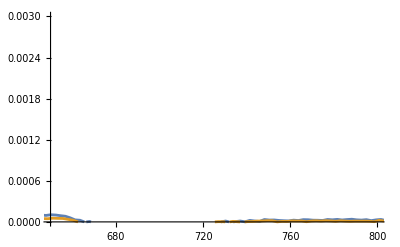

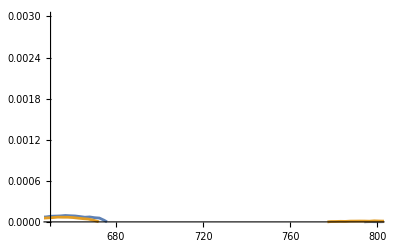

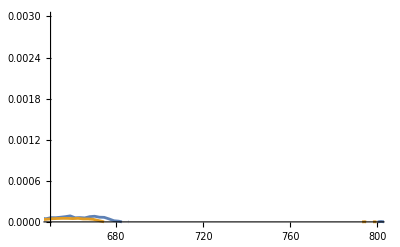

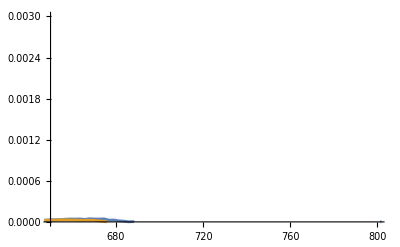

```mathematica
"monomeric2plots_0_1000_1.csv"
```

```mathematica
(*Figure 1 *)
```

```mathematica
(* Figure 1 *) 

timerange1=200+3000;
timerange2=1500+3000; 


monomeric1plots={spectramanrange[monomericdata[[1,1]],timerange1,timerange2],spectramanrange[monomericdata[[1,2]],timerange1,timerange2],spectramanrange[monomericdata[[1,3]],timerange1,timerange2],spectramanrange[monomericdata[[1,4]],timerange1,timerange2],spectramanrange[monomericdata[[1,5]],timerange1,timerange2]};
monomeric2plots={spectramanrange[monomericdata[[2,1]],timerange1,timerange2],spectramanrange[monomericdata[[2,2]],timerange1,timerange2],spectramanrange[monomericdata[[2,3]],timerange1,timerange2],spectramanrange[monomericdata[[2,4]],timerange1,timerange2],spectramanrange[monomericdata[[2,5]],timerange1,timerange2]};
monomeric3plots={spectramanrange[monomericdata[[3,1]],timerange1,timerange2],spectramanrange[monomericdata[[3,2]],timerange1,timerange2],spectramanrange[monomericdata[[3,3]],timerange1,timerange2],spectramanrange[monomericdata[[3,4]],timerange1,timerange2],spectramanrange[monomericdata[[3,5]],timerange1,timerange2]};

timerange1=200;
timerange2=1500; 


or1plots={spectramanrange[ordata[[1,1]],timerange1,timerange2],spectramanrange[ordata[[1,2]],timerange1,timerange2],spectramanrange[ordata[[1,3]],timerange1,timerange2],spectramanrange[ordata[[1,4]],timerange1,timerange2]};
or2plots={spectramanrange[ordata[[2,1]],timerange1,timerange2],spectramanrange[ordata[[2,2]],timerange1,timerange2],spectramanrange[ordata[[2,3]],timerange1,timerange2],spectramanrange[ordata[[2,4]],timerange1,timerange2]};
or3plots={spectramanrange[ordata[[3,1]],timerange1,timerange2],spectramanrange[ordata[[3,2]],timerange1,timerange2],spectramanrange[ordata[[3,3]],timerange1,timerange2],spectramanrange[ordata[[3,4]],timerange1,timerange2]};
or4plots={spectramanrange[ordata[[4,1]],timerange1,timerange2],spectramanrange[ordata[[4,2]],timerange1,timerange2],spectramanrange[ordata[[4,3]],timerange1,timerange2],spectramanrange[ordata[[4,4]],timerange1,timerange2]};

psi1plots={spectramanrange[psidata[[1,1]],timerange1,timerange2],spectramanrange[psidata[[1,2]],timerange1,timerange2],spectramanrange[psidata[[1,3]],timerange1,timerange2],spectramanrange[psidata[[1,4]],timerange1,timerange2]};
psi2plots={spectramanrange[psidata[[2,1]],timerange1,timerange2],spectramanrange[psidata[[2,2]],timerange1,timerange2],spectramanrange[psidata[[2,3]],timerange1,timerange2],spectramanrange[psidata[[2,4]],timerange1,timerange2]};
psi3plots={spectramanrange[psidata[[3,1]],timerange1,timerange2],spectramanrange[psidata[[3,2]],timerange1,timerange2],spectramanrange[psidata[[3,3]],timerange1,timerange2]};
psi0p2mWplots={spectramanrange[psipowerdata[[1,1]],timerange1,timerange2],spectramanrange[psipowerdata[[1,2]],timerange1,timerange2],spectramanrange[psipowerdata[[1,3]],timerange1,timerange2]};
psi0p35mWplots={spectramanrange[psipowerdata[[2,1]],timerange1,timerange2],spectramanrange[psipowerdata[[2,2]],timerange1,timerange2],spectramanrange[psipowerdata[[2,3]],timerange1,timerange2]};
psi0p45mWplots={spectramanrange[psipowerdata[[3,1]],timerange1,timerange2],spectramanrange[psipowerdata[[3,2]],timerange1,timerange2],spectramanrange[psipowerdata[[3,3]],timerange1,timerange2],spectramanrange[psipowerdata[[3,4]],timerange1,timerange2]};
ormv1plots={spectramanrange[ormvdata[[1,1]],timerange1,timerange2],spectramanrange[ormvdata[[1,2]],timerange1,timerange2],spectramanrange[ormvdata[[1,3]],timerange1,timerange2],spectramanrange[ormvdata[[1,4]],timerange1,timerange2]};
ormv1plots[[;;,;;,2]]=-ormv1plots[[;;,;;,2]];
ormv2plots={spectramanrange[ormvdata[[2,1]],timerange1,timerange2],spectramanrange[ormvdata[[2,2]],timerange1,timerange2],spectramanrange[ormvdata[[2,3]],timerange1,timerange2],spectramanrange[ormvdata[[2,4]],timerange1,timerange2]};
ormv2plots[[;;,;;,2]]=-ormv2plots[[;;,;;,2]];
ormv3plots={spectramanrange[ormvdata[[3,1]],timerange1,timerange2],spectramanrange[ormvdata[[3,2]],timerange1,timerange2],spectramanrange[ormvdata[[3,3]],timerange1,timerange2],spectramanrange[ormvdata[[3,4]],timerange1,timerange2]};
ormv3plots[[;;,;;,2]]=-ormv3plots[[;;,;;,2]];

Export["monomeric1plots.csv",{monomeric1plots[[1,;;,1]],monomeric1plots[[1,;;,2]],monomeric1plots[[2,;;,2]],monomeric1plots[[3,;;,2]],monomeric1plots[[4,;;,2]],monomeric1plots[[5,;;,2]]}]
Export["monomeric2plots.csv",{monomeric2plots[[1,;;,1]],monomeric2plots[[1,;;,2]],monomeric2plots[[2,;;,2]],monomeric2plots[[3,;;,2]],monomeric2plots[[4,;;,2]],monomeric2plots[[5,;;,2]]}]
Export["monomeric3plots.csv",{monomeric3plots[[1,;;,1]],monomeric3plots[[1,;;,2]],monomeric3plots[[2,;;,2]],monomeric3plots[[3,;;,2]],monomeric3plots[[4,;;,2]],monomeric3plots[[5,;;,2]]}]
Export["or1plots.csv",{or1plots[[1,;;,1]],or1plots[[1,;;,2]],or1plots[[2,;;,2]],or1plots[[3,;;,2]],or1plots[[4,;;,2]]}];
Export["psi1plots.csv",{psi1plots[[1,;;,1]],psi1plots[[1,;;,2]],psi1plots[[2,;;,2]],psi1plots[[3,;;,2]],psi1plots[[4,;;,2]]}];
Export["psi0p2mWplots.csv",{psi0p35mWplots[[1,;;,1]],psi0p35mWplots[[1,;;,2]],psi0p35mWplots[[2,;;,2]],psi0p35mWplots[[3,;;,2]]}];
Export["ormv1plots.csv",{ormv1plots[[1,;;,1]],ormv1plots[[1,;;,2]],ormv1plots[[2,;;,2]],ormv1plots[[3,;;,2]],ormv1plots[[4,;;,2]]}]



wavelength1=665;
wavelength2=708;


monomeric1plots={kineticrange[monomericdata[[1,1]],wavelength1,wavelength2],kineticrange[monomericdata[[1,2]],wavelength1,wavelength2],kineticrange[monomericdata[[1,3]],wavelength1,wavelength2],kineticrange[monomericdata[[1,4]],wavelength1,wavelength2],kineticrange[monomericdata[[1,5]],wavelength1,wavelength2]};
monomeric2plots={kineticrange[monomericdata[[2,1]],wavelength1,wavelength2],kineticrange[monomericdata[[2,2]],wavelength1,wavelength2],kineticrange[monomericdata[[2,3]],wavelength1,wavelength2],kineticrange[monomericdata[[2,4]],wavelength1,wavelength2],kineticrange[monomericdata[[2,5]],wavelength1,wavelength2]};
monomeric3plots={kineticrange[monomericdata[[3,1]],wavelength1,wavelength2],kineticrange[monomericdata[[3,2]],wavelength1,wavelength2],kineticrange[monomericdata[[3,3]],wavelength1,wavelength2],kineticrange[monomericdata[[3,4]],wavelength1,wavelength2],kineticrange[monomericdata[[3,5]],wavelength1,wavelength2]};

or1plots={kineticrange[ordata[[1,1]],wavelength1,wavelength2],kineticrange[ordata[[1,2]],wavelength1,wavelength2],kineticrange[ordata[[1,3]],wavelength1,wavelength2],kineticrange[ordata[[1,4]],wavelength1,wavelength2]};
or2plots={kineticrange[ordata[[2,1]],wavelength1,wavelength2],kineticrange[ordata[[2,2]],wavelength1,wavelength2],kineticrange[ordata[[2,3]],wavelength1,wavelength2],kineticrange[ordata[[2,4]],wavelength1,wavelength2]};
or3plots={kineticrange[ordata[[3,1]],wavelength1,wavelength2],kineticrange[ordata[[3,2]],wavelength1,wavelength2],kineticrange[ordata[[3,3]],wavelength1,wavelength2],kineticrange[ordata[[3,4]],wavelength1,wavelength2]};
or4plots={kineticrange[ordata[[4,1]],wavelength1,wavelength2],kineticrange[ordata[[4,2]],wavelength1,wavelength2],kineticrange[ordata[[4,3]],wavelength1,wavelength2],kineticrange[ordata[[4,4]],wavelength1,wavelength2]};
psi1plots={kineticrange[psidata[[1,1]],wavelength1,wavelength2],kineticrange[psidata[[1,2]],wavelength1,wavelength2],kineticrange[psidata[[1,3]],wavelength1,wavelength2],kineticrange[psidata[[1,4]],wavelength1,wavelength2]};
psi2plots={kineticrange[psidata[[2,1]],wavelength1,wavelength2],kineticrange[psidata[[2,2]],wavelength1,wavelength2],kineticrange[psidata[[2,3]],wavelength1,wavelength2],kineticrange[psidata[[2,4]],wavelength1,wavelength2]};
psi3plots={kineticrange[psidata[[3,1]],wavelength1,wavelength2],kineticrange[psidata[[3,2]],wavelength1,wavelength2],kineticrange[psidata[[3,3]],wavelength1,wavelength2]};
psi0p2mWplots={kineticrange[psipowerdata[[1,1]],wavelength1,wavelength2],kineticrange[psipowerdata[[1,2]],wavelength1,wavelength2],kineticrange[psipowerdata[[1,3]],wavelength1,wavelength2]};
psi0p35mWplots={kineticrange[psipowerdata[[2,1]],wavelength1,wavelength2],kineticrange[psipowerdata[[2,2]],wavelength1,wavelength2],kineticrange[psipowerdata[[2,3]],wavelength1,wavelength2]};
psi0p45mWplots={kineticrange[psipowerdata[[3,1]],wavelength1,wavelength2],kineticrange[psipowerdata[[3,2]],wavelength1,wavelength2],kineticrange[psipowerdata[[3,3]],wavelength1,wavelength2],kineticrange[psipowerdata[[3,4]],wavelength1,wavelength2]};


ormv1plots={kineticrange[ormvdata[[1,1]],wavelength1,wavelength2],kineticrange[ormvdata[[1,2]],wavelength1,wavelength2],kineticrange[ormvdata[[1,3]],wavelength1,wavelength2],kineticrange[ormvdata[[1,4]],wavelength1,wavelength2]};
ormv2plots={kineticrange[ormvdata[[2,1]],wavelength1,wavelength2],kineticrange[ormvdata[[2,2]],wavelength1,wavelength2],kineticrange[ormvdata[[2,3]],wavelength1,wavelength2],kineticrange[ormvdata[[2,4]],wavelength1,wavelength2]};
ormv3plots={kineticrange[ormvdata[[3,1]],wavelength1,wavelength2],kineticrange[ormvdata[[3,2]],wavelength1,wavelength2],kineticrange[ormvdata[[3,3]],wavelength1,wavelength2],kineticrange[ormvdata[[3,4]],wavelength1,wavelength2]};

or2plots[[;;,;;,2]]=-or2plots[[;;,;;,2]];
or3plots[[;;,;;,2]]=-or3plots[[;;,;;,2]];

ormv1plots[[;;,;;,2]]=-ormv1plots[[;;,;;,2]]*1.2;
ormv2plots[[;;,;;,2]]=-ormv2plots[[;;,;;,2]]*1.2;
ormv3plots[[;;,;;,2]]=-ormv3plots[[;;,;;,2]]*1;
ormv3plots[[;;,;;,1]]=100+ormv3plots[[;;,;;,1]];
ormv1plots[[;;,;;,1]]=200+ormv1plots[[;;,;;,1]];

Export["monomeric1plots_wavelength.csv",{monomeric1plots[[1,;;,1]],monomeric1plots[[1,;;,2]],monomeric1plots[[2,;;,2]],monomeric1plots[[3,;;,2]],monomeric1plots[[4,;;,2]],monomeric1plots[[5,;;,2]]}];
Export["monomeric2plots_wavelength.csv",{monomeric2plots[[1,;;,1]],monomeric2plots[[1,;;,2]],monomeric2plots[[2,;;,2]],monomeric2plots[[3,;;,2]],monomeric2plots[[4,;;,2]],monomeric2plots[[5,;;,2]]}];
Export["monomeric3plots_wavelength.csv",{monomeric3plots[[1,;;,1]],monomeric3plots[[1,;;,2]],monomeric3plots[[2,;;,2]],monomeric3plots[[3,;;,2]],monomeric3plots[[4,;;,2]],monomeric3plots[[5,;;,2]]}];
Export["or1plots_wavelength.csv",{or1plots[[1,;;,1]],or1plots[[1,;;,2]],or1plots[[2,;;,2]],or1plots[[3,;;,2]],or1plots[[4,;;,2]]}];
Export["or1plotsmv_wavelength.csv",{ormv1plots[[1,;;,1]],ormv1plots[[1,;;,2]],ormv1plots[[2,;;,2]],ormv1plots[[3,;;,2]],ormv1plots[[4,;;,2]]}];
Export["psi1plots_wavelength.csv",{psi1plots[[1,;;,1]],psi1plots[[1,;;,2]],psi1plots[[2,;;,2]],psi1plots[[3,;;,2]],psi1plots[[4,;;,2]]}];
Export["psi0p2mWplots_wavelength.csv",{psi0p35mWplots[[1,;;,1]],psi0p35mWplots[[1,;;,2]],psi0p35mWplots[[2,;;,2]],psi0p35mWplots[[3,;;,2]]}];
```